Number of Dissertations with Newspaper Appearances
Ian Milligan, UW
September 2012

```mathematica
test=Import["/users/ianmilligan/desktop/test.xlsx"];
```

```mathematica
test//TableForm
```

Globe and Mail
23.
15.
20.
17.
27.
24.
39.
19.
34.
28.
30.
23.
30.
27. | Toronto Star
14.
13.
15.
11.
18.
13.
23.
16.
23.
22.
20.
21.
28.
23. | Toronto Telegram
5.
5.
12.
4.
7.
8.
8.
4.
7.
7.
12.
9.
8.
7. | Montreal Gazette
15.
8.
17.
14.
19.
16.
24.
15.
20.
20.
20.
16.
15.
14. | Ottawa Citizen
10.
13.
10.
13.
15.
12.
29.
17.
15.
15.
17.
13.
18.
8.

```mathematica
test
```

{{{Globe and Mail,23.,15.,20.,17.,27.,24.,39.,19.,34.,28.,30.,23.,30.,27.},{Toronto Star,14.,13.,15.,11.,18.,13.,23.,16.,23.,22.,20.,21.,28.,23.},{Toronto Telegram,5.,5.,12.,4.,7.,8.,8.,4.,7.,7.,12.,9.,8.,7.},{Montreal Gazette,15.,8.,17.,14.,19.,16.,24.,15.,20.,20.,20.,16.,15.,14.},{Ottawa Citizen,10.,13.,10.,13.,15.,12.,29.,17.,15.,15.,17.,13.,18.,8.}}}

```mathematica
globeAppearances={23.,15.,20.,17.,27.,24.,39.,19.,34.,28.,30.,23.,30.,27};
starAppearances={14.,13.,15.,11.,18.,13.,23.,16.,23.,22.,20.,21.,28.,23.};
telegramAppearances={5.,5.,12.,4.,7.,8.,8.,4.,7.,7.,12.,9.,8.,7.};
gazetteAppearances={15.,8.,17.,14.,19.,16.,24.,15.,20.,20.,20.,16.,15.,14};
citizenAppearances={10.,13.,10.,13.,15.,12.,29.,17.,15.,15.,17.,13.,18.,8.};
```

```mathematica
dataset={globeAppearances,starAppearances,telegramAppearances,gazetteAppearances,citizenAppearances}
```

{{23.,15.,20.,17.,27.,24.,39.,19.,34.,28.,30.,23.,30.,27},{14.,13.,15.,11.,18.,13.,23.,16.,23.,22.,20.,21.,28.,23.},{5.,5.,12.,4.,7.,8.,8.,4.,7.,7.,12.,9.,8.,7.},{15.,8.,17.,14.,19.,16.,24.,15.,20.,20.,20.,16.,15.,14},{10.,13.,10.,13.,15.,12.,29.,17.,15.,15.,17.,13.,18.,8.}}

```mathematica
Needs["PlotLegends`"];
```

```mathematica
yearlist=Range[1997,2010];
```

```mathematica
globeYear=Thread[{yearlist,globeAppearances}];
starYear=Thread[{yearlist,starAppearances}];
telegramYear=Thread[{yearlist,telegramAppearances}];
gazetteYear=Thread[{yearlist,gazetteAppearances}];
citizenYear=Thread[{yearlist,citizenAppearances}];
yearDataset={globeYear,starYear,telegramYear,gazetteYear,citizenYear};
```

```mathematica
dissertationNumbers={87,67,83,69,73,78,89,65,71,69,63,70,70,69};
```

```mathematica
percentageGlobe=globeAppearances/dissertationNumbers;
percentageStar=starAppearances/dissertationNumbers;
percentageTelegram=telegramAppearances/dissertationNumbers;
percentageGazette=gazetteAppearances/dissertationNumbers;
percentageCitizen=citizenAppearances/dissertationNumbers;
```

```mathematica
Mean[{0.26,0.22,0.24,0.25,0.37,0.31}]
```

```mathematica
0.27499999999999997 (** percentage before DB in Globe **)
```

```mathematica
Mean[{0.478,0.405,0.476,0.328,0.429,9/23}]
```

0.417884

```mathematica
percentageglobeYear//NumberForm
```

{{1997,0.264368},{1998,0.223881},{1999,0.240964},{2000,0.246377},{2001,0.369863},{2002,0.307692},{2003,0.438202},{2004,0.292308},{2005,0.478873},{2006,0.405797},{2007,0.47619},{2008,0.328571},{2009,0.428571},{2010,9/23}}

```mathematica
percentagestarYear//NumberForm
```

{{1997,0.16092},{1998,0.19403},{1999,0.180723},{2000,0.15942},{2001,0.246575},{2002,0.166667},{2003,0.258427},{2004,0.246154},{2005,0.323944},{2006,0.318841},{2007,0.31746},{2008,0.3},{2009,0.4},{2010,0.333333}}

```mathematica
Mean[{0.16,0.19,0.18,0.16,0.25,0.17}]
```

0.185

```mathematica
Mean[{0.323,0.318,0.317,0.3,0.4,0.33}]
```

0.331333

```mathematica
percentageglobeYear=Thread[{yearlist,percentageGlobe}];
percentagestarYear=Thread[{yearlist,percentageStar}];
percentagetelegramYear=Thread[{yearlist,percentageTelegram}];
percentagegazetteYear=Thread[{yearlist,percentageGazette}];
percentagecitizenYear=Thread[{yearlist,percentageCitizen}];
percentageyearDataset={percentageglobeYear,percentagestarYear,percentagetelegramYear,percentagegazetteYear,percentagecitizenYear};
```

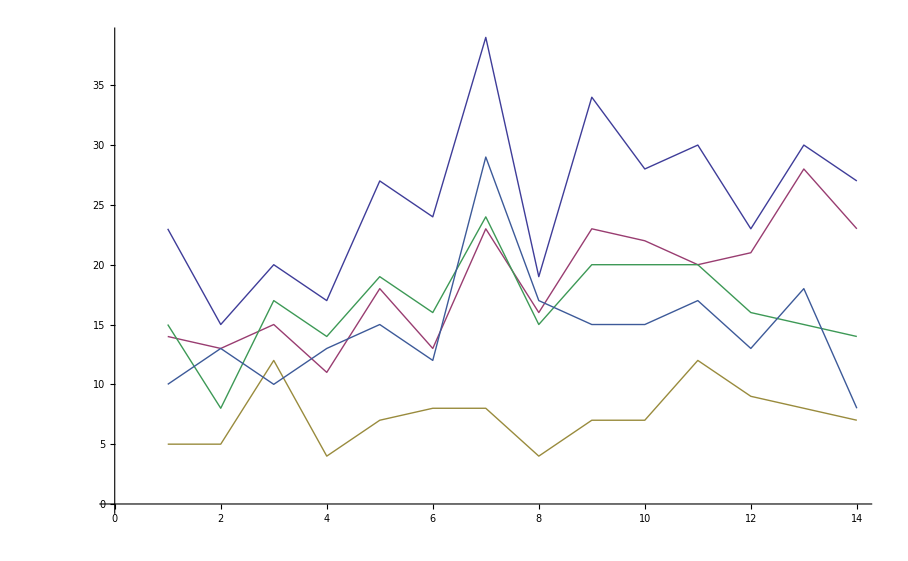

```mathematica
ListLinePlot[dataset]
```

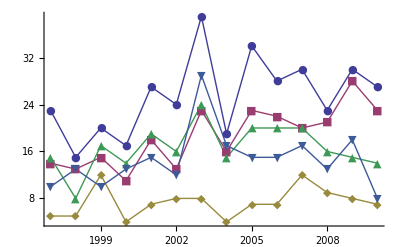

```mathematica
ListLinePlot[yearDataset,Joined->True,PlotRange->All,LegendPosition->{1.1,-0.4},PlotLegend->{"Globe","Star","Gazette","Citizen","Telegram"},PlotStyle->Thick,Axes->True,AxesOrigin->{1997,0},PlotMarkers->{Automatic,Large}]
```

```mathematica
ListLinePlot[percentageyearDataset,Joined->True,PlotRange->All,LegendPosition->{1.1,-0.4},PlotLegend->{"Globe","Star","Telegram","Gazette","Citizen"},PlotStyle->Thick,Axes->True,AxesOrigin->{1997,0},PlotMarkers->{Automatic,Large}]
```